```mathematica
Considere a função f(x)=(sin(x))/x para x>=0  ([0,∞])
a)Qual seria um bom valor x∞? E para x0?
b)Quantos pontos são necessários para representar f(x) no intervalo [x0, x∞]?
c)Quanto vale f(x0) e f(x∞)?
```

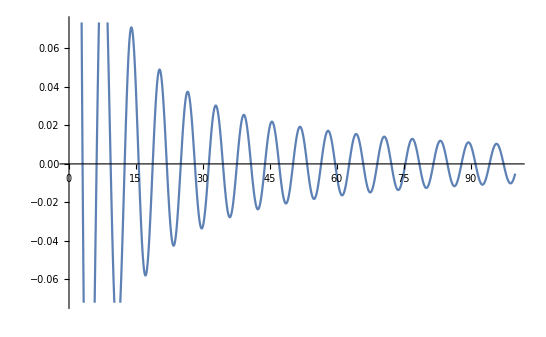

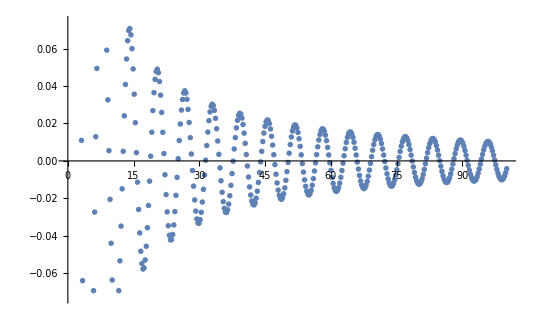

```mathematica
(*
Definição da função
*)
f[x_]:=Sin[x]/x;
Plot[f[x],{x,0.1,100}]

(*
Definição de parâmetros de discretização
*)
np = 400;
ni=np-1;
dx=100/ni;

(*
Definição dos pontos do gráfico
*)
xv=Table[i,{i,0.1,101,dx}];
fxv=Table[{xv[[i]],f[xv[[i]]]},{i,1,np}];
ListPlot[fxv]
```

```mathematica
f[0.1]
```

0.998334

```mathematica
N[f[500]]
```

-0.000935544

```mathematica
Respostas:

a)Um bom valor para x0 seria 0.1 , uma vez que o  valor de f(0.1) é um valor muito próximo de 1, que é o lim (sen(x))/x, x->0.
E um bom valor para x∞ seria 500, pois f(500) é um valor muito próximo de 0, que é o valor de lim (sen(x))/x, x-> ∞

b)Para o intervalo da função [0.1, 500], 400 é uma boa quantidade de pontos para representar a função pois a função fica clara 
com essa quantidade de pontos

c)f(x0) = f(0.1) = 0.998334
   f(x∞) = f(500) = -0.000935544
```